# HyperBloch package tutorial

## Getting started

This notebook provides solved exercises aimed to introduce the functionality of the  HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices. It is intended to be used in tandem with the Getting started with the HyperBloch package tutorial  on the HyperCells&HyperBloch website.  In this tutorial we will see how the cell, model and supercell model graphs, constructed through HyperBloch’s sister package HyperCells, can be imported and visualized in the Poincaré disk. Moreover, we go through the intended workflow for the construction of corresponding Abelian Bloch Hamiltonians in order to demonstrate the supercell method through density of states calculations.

## Preliminaries:

### Remarks:

Before using the getting started with the HyperBloch package notebook:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website HyperCells&HyperBloch installation.

Make sure that the required files .hcc,  .hcm and .hcs files are in the current directory. This entails files:

(2,8,8)_T2.6_3.hcc
(2,8,8)_T3.11_3.hcc
{8,8}-tess_T2.6_3.hcm
{8,8}-tess_T2.6_3_sc-T3.11.hcs

In case no such files exist in your current directory, please follow the instructions in the  Getting started with the HyperBloch package,  or download the files there.

### Documentation:

You may want to take a look at the basic usage guide of the HyperBloch package or the available functions within the package, respectively:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

## Preparations:

### Load the HyperBloch package:

The HyperBloch package can be loaded as follows:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

Set the directory of the needed HyperCells files remarked above, which is assumed to be the directory of this file:

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Primitive cell:

### Import the cell graph:

The cell graph defines a maximally symmetric triangular tessellation of the corresponding connected and compactified translation unit cell.
We import it with the function ImportCellGraphString:

```mathematica
pcell=ImportCellGraphString[Import["(2,8,8)_T2.6_3.hcc"]];
```

Note the use of the  Import function inside theImportCellGraphString function. This is necessary, because the exported file is a text file, which contains the string representation of the cell graph. The Import function is used to read the file, while the ImportCellGraphString function is used to parse the string and construct the cell graph. Alternatively, we could have used the function ExportString in GAP to export the cell graph as a string, copied the string into a Mathematica notebook, and then used the ImportCellGraphString function directly to parse the string and construct the cell graph.

### Import the model graph:

The model graph is derived from cell graph. In our case it defines a nearest-neighbor graph of the {8,8}-tessellation of the hyperbolic plane restricted to the primitive cell. 
It can be imported analogously, but requires the use of the function ImportModelGraphString in order to parse the string and construct the model graph instead:

```mathematica
pcmodel=ImportModelGraphString[Import["{8,8}-tess_T2.6_3.hcm"]];
```

### Visualize the model graph:

The graph representation of the model on the primitive cell can be visualized with the function  VisualizeModelGraph:

```mathematica
VisualizeModelGraph[pcmodel,
CellGraph->pcell,
Elements-><|
	ShowCellBoundary->{ShowEdgeIdentification->True},
	ShowCellGraphFlattened->{}
|>,
ImageSize->300,
NumberOfGenerations->2]
```

-Graphics-

We have passed the cell graph to the option CellGraph which enables us to indicate the unit cell boundary through the function ShowCellBoundary. Moreover, the boundary segments are indicated together with the associated (composite) translation and colored according to the boundary identification. The function ShowCellGraphFlattened is used to shown all edges connecting pairs of vertices as hyperbolic geodesics in the Poincaré disk.

### Construct the Hamiltonian:

In order to construct the Abelian Bloch Hamiltonian, parameters need to be assigned to the vertices and the edges in the model graph. This takes a very compact form for an elementary nearest-neighbour tight-binding model. In order to illustrate the procedure, we will start with the most general assignment strategy and demonstrate the compact form afterwards. (On a first read one may want to skip the subsubsection General strategy and resume at the subsubsection Compact strategy.)

#### General strategy:

##### Number of orbitals:

Every (supercell) model graph can be equipped with multiple orbitals per site, and even with a varying number of orbitals at each site. We will construct more involved models with multiple orbitals per site in the  HyperBloch Higher-order topology tutorial, for now, however, we will set the number of orbitals to one:

```mathematica
norbits = 1;
```

##### On-site terms:

On-site terms in the Hamiltonian are associated with vertices in the (supercell) model graph. As such, it is instructive to explicitly print these vertices by using the function VertexList, which takes as argument the graph representation:

```mathematica
VertexList@pcmodel["Graph"]
```

{{3,1}}

There is only one vertex present in the graph which corresponds to one site within the primitive cell of the {8,8}-lattice. The vertex labels of the model graph are of a particular form, the interested reader may find the detailed description here HCModelGraph. We choose to set the on-site term to zero by associating the list of vertices with a list of zeros using an Associtation :

```mathematica
mVec =ConstantArray[0,1]; 
onsitePC=AssociationThread[VertexList@pcmodel["Graph"]->mVec];
```

##### Hopping terms:

The hopping terms are associated with edges in the (supercell) model graph. Similarly to the on-site terms, it is useful to explicitly print the edges using the function EdgeList,  which takes as argument the graph representation:

```mathematica
EdgeList@pcmodel["Graph"]
```

{{3,1}{3,1}{1,{{1,1},1,5}},{3,1}{3,1}{1,{{1,2},4,8}},{3,1}{3,1}{1,{{1,3},2,6}},{3,1}{3,1}{1,{{1,4},3,7}}}

Each element in the list is a DirectedEdge, connecting a pair of vertices. The interested reader may find the detailed description of the EdgeTags (nested list above the arrows) here HCModelGraph. We choose to set the hopping terms to a constant real value -1 for all edges by associating the edge list with a list of constant values:

```mathematica
nnHoppingVec=ConstantArray[-1,4];
hoppingPC=AssociationThread[EdgeList@pcmodel["Graph"]->nnHoppingVec];
```

If we would consider a more involved model it might be helpful to look at the translation operators associated with the edges:

```mathematica
pcmodel["EdgeTranslations"]
```

{g1,g4,g2,g3}

In our particular case, all edges are associated with inter-cell hopping amplitudes. The HyperBloch package is equipped with elaborate visualization tools of cell, model and supercell model graphs which can further guide the construction of models in more advanced settings. We will exploit these in subsequent tutorials

##### Hamiltonian:

The Abelian Bloch Hamiltonian can now be set up by passing the model graph and the corresponding coupling constants specified above to as arguments to the function AbelianBlochHamiltonian or alternatively AbelianBlochHamiltonianExpression, the former returns the Hamiltonian as a function of momenta. We choose to use the latter for now, in order to print a symbolic expression of the Hamiltonian:

```mathematica
Hpc=AbelianBlochHamiltonianExpression[pcmodel,norbits,onsitePC,hoppingPC, k]
```

```mathematica
FullSimplify[Hpc]
```

{{-2 (Cos[k[1]]+Cos[k[2]]+Cos[k[3]]+Cos[k[4]])}}

#### Compact strategy:

The simplicity of the specified elementary nearest-neighbor hopping model reduces the procedure for the construction of the Hamiltonian to just one line of code. We can use the function AbelianBlochHamiltonian, which returns the Hamiltonian as a function of momenta:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,0&,-1&]
```

Function[{k1,k2,k3,k4},{{-ⅇ^(-ⅈ k1)-ⅇ^(ⅈ k1)-ⅇ^(-ⅈ k2)-ⅇ^(ⅈ k2)-ⅇ^(-ⅈ k3)-ⅇ^(ⅈ k3)-ⅇ^(-ⅈ k4)-ⅇ^(ⅈ k4)}}]

The function can be compiled for more efficient evaluation by specifying the option CompileFuncton:

```mathematica
Hpccf=AbelianBlochHamiltonian[pcmodel,1,0&,-1&,CompileFunction->True];
```

### Density of states:

#### Eigenvalues:

To compute the density of states, we can now take advantage of the independence of different momentum sectors and therefore parallelize the computation of the eigenvalues. We take a set of Nptsrandom samples in momentum space and partition this set into Nruns subsets. The dimension of Brillouin zone is defined by the genus of the compactified primitive cell and is 2×genus, which we specify by passing the genus as an argument. As such, we compute the eigenvalues with the following function:

```mathematica
ComputeEigenvalues[cfH_,Npts_,Nruns_, genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@RandomReal[{-Pi,Pi},2genus]],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

We compute the Eigenvalues with a set of  10^6 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evals=ComputeEigenvalues[Hpccf,10^6,32, pcmodel["Genus"]];
```

#### Visualization:

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.005, (this might take a minute):

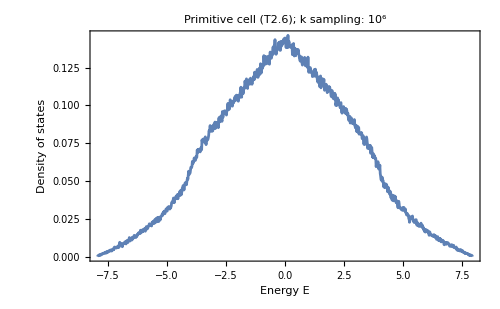

```mathematica
SmoothHistogram[evals,0.005,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},LabelStyle->20,
PlotLabel->"Primitive cell (T2.6); k sampling: 10^6",PlotRange->All]
```

## First supercell:

### Import the cell and supercell model graph:

The cell graph for the compactified translation supercell can be imported like the one for the primitive cell through the function ImportCellGraphString:

```mathematica
scell=ImportCellGraphString[Import["(2,8,8)_T3.11_3.hcc"]];
```

The supercell model graph is derived from cell graph can be imported analogously, but requires the use of the function ImportSupercellModelGraphString instead:

```mathematica
scmodel=ImportSupercellModelGraphString[Import["{8,8}-tess_T2.6_3_sc-T3.11.hcs"]];
```

### Visualize the supercell model graph:

We can visualize the graph representation of the model on the supercell analogously to the primitive cell:

```mathematica
VisualizeModelGraph[scmodel,
CellGraph->scell,
Elements-><|
	ShowCellBoundary->{ShowEdgeIdentification->True},
	ShowCellGraphFlattened->{}
|>,
NumberOfGenerations->3,ImageMargins->0,
ImagePadding->10,ImageSize->300]
```

-Graphics-

The vertex and edge labels of the supercell model graph are of a particular form, the interested reader may find the detailed description here HCSupercellModelGraph.

### Hamiltonian and density of states:

The construction of the model on the primitive cell already encompasses all the model specification for the supercell. In order to construct the elementary nearest-neighbor tight-binding model on the supercell, we just need to replace the model graph with the supercell model graph in the first argument in the function AbelianBlochHamiltonian (or alternatively AbelianBlochHamiltonianExpression). In addition, we also need to specify the associated model graph with the option PCModel. This captures some of the higher-dimensional irreducible representations on the original primitive cell:

```mathematica
Hsccf=AbelianBlochHamiltonian[scmodel,1,0&,-1&,PCModel->pcmodel,CompileFunction->True];
```

We compute the Eigenvalues with a set of  2·10^5 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evssc=ComputeEigenvalues[Hsccf,2 10^5,32];
```

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.005, (this might take a minute):

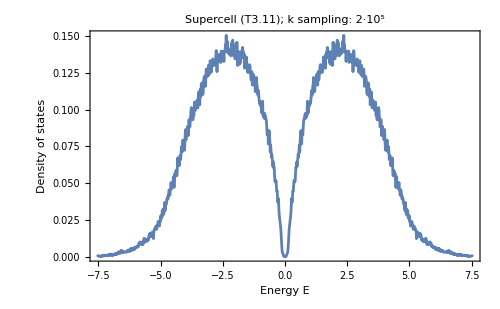

```mathematica
SmoothHistogram[evals,0.005,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},LabelStyle->20,
PlotLabel->"Supercell (T3.11); k sampling: 2·10^5",PlotRange->All]
```

```mathematica
NotebookSave[]
```